## Solving Linear Stability Analysis for Line Model

Derive Eqn of Motion

```mathematica
beam[]:=Module[{},
Null
]
```

```mathematica
eomRho[beta_,eta_,omegav_,mu_,vz_,k0_,m_]:=Module[{rhoM,epsilonM},

rhoM={{1,epsilonM[z]},{Conjugate@epsilonM[z],0}};

I vz D[rhoM,z]=m k0 √(1-vz)rhoM-beta*eta*omegav/2 (PauliMatrix[3].rhoM-rhoM.PauliMatrix[3])(*+*)

]
```

```mathematica
PauliMatrix[3].{{1,epsilon},{Conjugate@epsilon,0}}-{{1,epsilon},{Conjugate@epsilon,0}}.PauliMatrix[3]//MatrixForm
```

(0 | 2 epsilon
-2 Conjugate[epsilon] | 0)

```mathematica
{{1,epsiloni},{Conjugate@epsiloni,0}}.{{1,epsilonj},{Conjugate@epsilonj,0}}-{{1,epsilonj},{Conjugate@epsilonj,0}}.{{1,epsiloni},{Conjugate@epsiloni,0}}//MatrixForm
```

(-epsilonj Conjugate[epsiloni]+epsiloni Conjugate[epsilonj] | -epsiloni+epsilonj
Conjugate[epsiloni]-Conjugate[epsilonj] | epsilonj Conjugate[epsiloni]-epsiloni Conjugate[epsilonj])

Eigensystem

with four beams

```mathematica
(*ClearAll[vz,k0,alpha,lambda,vx]*)
```

```mathematica
vz=0.5
k0=omegav/10
alpha=0.8
lambda=0
vx=√(1-vz^2)
```

0.5

omegav/10

0.8

0

0.866025

```mathematica
(* The 'Hamiltonian' for the variables *)
upsilon=1/vz{
{m k0 vx + lambda - eta omegav + (1-alpha)chi,0,-chi,alpha chi},
{0,m k0 vx + lambda + eta omegav +(1-alpha)chi,-chi,alpha chi},
{-chi,alpha chi,-m k0 vx + lambda-eta omegav+(1-alpha)chi,0},
{-chi,alpha chi,0,-m k0 vx + lambda +eta omegav + (1-alpha)chi}
};
%//MatrixForm
```

(2. (100+0.2 chi-eta omegav+0.0866025 m omegav) | 0. | -2. chi | 1.6 chi
0. | 2. (100+0.2 chi+eta omegav+0.0866025 m omegav) | -2. chi | 1.6 chi
-2. chi | 1.6 chi | 2. (100+0.2 chi-eta omegav-0.0866025 m omegav) | 0.
-2. chi | 1.6 chi | 0. | 2. (100+0.2 chi+eta omegav-0.0866025 m omegav))

```mathematica
rMatrix=1/2{
{1,-alpha,1,-alpha},
{1,alpha,1,alpha},
{1,-alpha,-1,alpha},
{1,alpha,-1,-alpha}
};
%//MatrixForm
```

(1/2 | -0.4 | 1/2 | -0.4
1/2 | 0.4 | 1/2 | 0.4
1/2 | -0.4 | -1/2 | 0.4
1/2 | 0.4 | -1/2 | -0.4)

```mathematica
upsilonTransformed[eta_,chi_,m_,omegav_]=rMatrix.upsilon.Inverse[rMatrix]/omegav//FullSimplify;
```

```mathematica
upsilonTransformed[eta,chi,m,omegav]//MatrixForm
```

((200.+6.93889×10^-17 chi)/omegav | 0.-2. eta-(6.93889×10^-17 chi)/omegav | 0.+0.173205 m | 0.
0.-2. eta-(3.6 chi)/omegav | (200.+0.4 chi)/omegav | 0. | 0.+0.173205 m
0.+0.173205 m | 0. | (200.+0.8 chi)/omegav | 0.-2. eta+(5.55112×10^-17 chi)/omegav
0. | 0.+0.173205 m | 0.-2. eta+(3.6 chi)/omegav | (200.+0.4 chi)/omegav)

```mathematica
(*eigenValues[eta_,chi_,m_,omegav_]:=Eigenvalues[upsilonTransformed[eta,chi,m,omegav]]*)
eigenValues[eta_,chi_,m_,omegav_]=Eigenvalues[upsilon];
```

```mathematica
pltFunction[chi_,m_]=eigenValues[1,chi,m,1][[4]]
```

Root[1.59968×10^9+1.27987×10^7 chi+30794.9 chi^2+23.296 chi^3-5.55112×10^-16 chi^4-1.33227×10^-15 chi^2 m-1.38778×10^-17 chi^3 m-2400.24 m^2-9.6 chi m^2-0.0048 chi^2 m^2+2.22045×10^-16 m^3+0.0009 m^4+(-3.19968×10^7-191994. chi-314.24 chi^2-0.128 chi^3-1.81899×10^-12 m-7.10543×10^-15 chi m+2.77556×10^-17 chi^2 m+24. m^2+0.048 chi m^2) #1+(239992.+960. chi+0.8 chi^2+7.10543×10^-15 m+1.38778×10^-17 chi m-0.06 m^2) #1^2+(-800.-1.6 chi) #1^3+1. #1^4&,4]

```mathematica
pltDensity1=DensityPlot[Max[Im@pltFunction[x,y^2]],{x,0,500},{y,0,50},PlotLegends->Automatic,PlotLabel->"Maximum value of imaginary part of eigenvalues",ImageSize->600,FrameLabel->{"μ/ω_v","√(|m|)"},MaxRecursion->2,PlotPoints->100,ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
(*Export["/Users/leima/GitHub/NeuPhysics/codebase-lite/mma/linear-stability-analysis/kappa.png",pltDensity1]*)
```

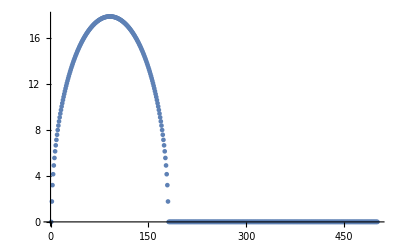

```mathematica
ListPlot[
Table[
Max[
Im@eigenValues[1,x,150,1]
],
{x,0,500,1}]
]
```

Using the matrix from the paper

```mathematica
LambdaMatrix[eta_,mu_,m_]:=1/vz{
{0,-eta omegav,m k0 vx,0},
{-eta omegav-(1+alpha)mu,(1-alpha)mu,0,m k0 vx},
{m k0 vx,0,2(1-alpha)mu,-eta omegav},
{0,m k0 vx,-eta omegav + (1+alpha)mu,(1-alpha)mu}
}/.{omegav->1};
```

```mathematica
LambdaMatrix[eta,mu,m]-eig IdentityMatrix[4]//MatrixForm
```

(0.-eig | -2. eta | 0.173205 m | 0.
2. (-eta-1.8 mu) | -eig+0.4 mu | 0. | 0.173205 m
0.173205 m | 0. | -eig+0.8 mu | -2. eta
0. | 0.173205 m | 2. (-eta+1.8 mu) | -eig+0.4 mu)

```mathematica
eigCharaEqn[eta_,mu_,m_]=Det[
LambdaMatrix[eta,mu,m]-eig IdentityMatrix[4]
]==0
```

0.+eig^4-8. eig^2 eta^2+16. eta^4-0.06 eig^2 m^2-0.24 eta^2 m^2+0.0009 m^4-1.6 eig^3 mu+6.4 eig eta^2 mu+0.048 eig m^2 mu+0.8 eig^2 mu^2+5.76 eig eta mu^2-53.12 eta^2 mu^2-0.0048 m^2 mu^2-0.128 eig mu^3-2.304 eta mu^3==0

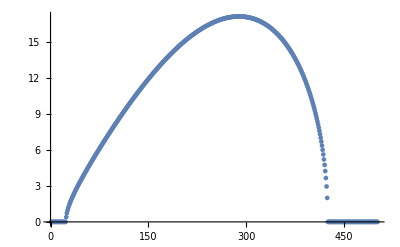

```mathematica
ListPlot[
Table[
Max[
Im@eig/.NSolve[
eigCharaEqn[1,x,1000],
eig
]
],
{x,0,500,1}]
]
```

```mathematica
pltPaperFunction[mu_,m_]=Eigenvalues[LambdaMatrix[-1,mu,m]]
```

{Root[17777.8-266.667 m^2+1. m^4-59022.2 mu^2-5.33333 m^2 mu^2+2560. mu^3+(7111.11 mu+53.3333 m^2 mu-6400. mu^2-142.222 mu^3) #1+(-8888.89-66.6667 m^2+888.889 mu^2) #1^2-1777.78 mu #1^3+1111.11 #1^4&,1],Root[17777.8-266.667 m^2+1. m^4-59022.2 mu^2-5.33333 m^2 mu^2+2560. mu^3+(7111.11 mu+53.3333 m^2 mu-6400. mu^2-142.222 mu^3) #1+(-8888.89-66.6667 m^2+888.889 mu^2) #1^2-1777.78 mu #1^3+1111.11 #1^4&,2],Root[17777.8-266.667 m^2+1. m^4-59022.2 mu^2-5.33333 m^2 mu^2+2560. mu^3+(7111.11 mu+53.3333 m^2 mu-6400. mu^2-142.222 mu^3) #1+(-8888.89-66.6667 m^2+888.889 mu^2) #1^2-1777.78 mu #1^3+1111.11 #1^4&,3],Root[17777.8-266.667 m^2+1. m^4-59022.2 mu^2-5.33333 m^2 mu^2+2560. mu^3+(7111.11 mu+53.3333 m^2 mu-6400. mu^2-142.222 mu^3) #1+(-8888.89-66.6667 m^2+888.889 mu^2) #1^2-1777.78 mu #1^3+1111.11 #1^4&,4]}

```mathematica
Im@pltPaperFunction[1,4]
Max[Im@pltPaperFunction[1,4]]
```

{0,0,-1.78628,1.78628}

1.78628

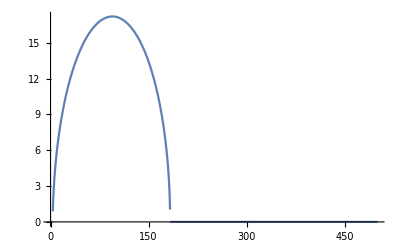

```mathematica
Plot[
Max[Im@pltPaperFunction[x,30]],
{x,0,500}]
```

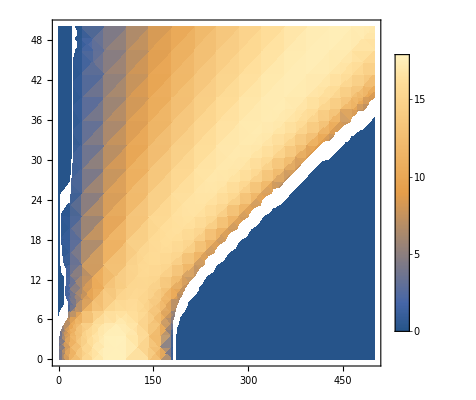

```mathematica
DensityPlot[
Max[Im@pltPaperFunction[x,y^2]],
{x,0,500},{y,0,50},PlotLegends->Automatic]
```

```mathematica
Inverse[rMatrix].LambdaMatrix[eta,mu,m].rMatrix//FullSimplify//MatrixForm
```

((-eta+mu-alpha mu+k0 m vx)/vz | 0 | -mu/vz | (alpha mu)/vz
0 | (eta+mu-alpha mu+k0 m vx)/vz | -mu/vz | (alpha mu)/vz
-mu/vz | (alpha mu)/vz | -(eta+(-1+alpha) mu+k0 m vx)/vz | 0
-mu/vz | (alpha mu)/vz | 0 | (eta+mu-alpha mu-k0 m vx)/vz)